```mathematica
filelist=("E:\\_time_varying_data\\SmokeSim\\tif\\dsSmoke."<>IntegerString[#,10,3]<>".tif")&/@Range[0,499];
d=Import[filelist[[#]],"Image3D"]&/@Range[1,500];
offset=9;
tf=ColorData["RedGreenSplit"]
tffilelist=("E:\\_time_varying_data\\SmokeSim\\DSSmokeSideways100500\\dsSmoke."<>IntegerString[#,10,3]<>".tfi")&/@Range[0,499];
bincount=256;
i=160;
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//RGBColor/@#&;
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
CloseKernels[];
LaunchKernels[8];
```

ColorDataFunction[…]

```mathematica
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[h[[2]]]-1)];
sum:=Total[h[[2]]];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;
probability[i_]:=N[h[[2]][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];If[p≠0,-p*Log[p],0]];
op=Module[{t},t=entropy[#];If[t!=0,1./t,0]]&/@intensityfunction//Rescale;
op2=entropy[#]&/@intensityfunction//Rescale;
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
b=Flatten[ImageData[std]];
numofbins=Length[h[[2]]]-1;
bins=ConstantArray[0,Length[h[[2]]]];
sumstd=ConstantArray[0,Length[h[[2]]]];
Table[j=IntegerPart[a[[i]]*numofbins]+1;bins[[j]]++;sumstd[[j]]+=b[[i]],{i,1,Length[a]}];
stds=sumstd/bins;
volatility[i_]:=N[stds[[hist[i]]]];
temporalentropy[i_]:=Module[{p},p=volatility[i];If[p≠0,-p*Log[p],0]];
op3=Module[{t},t=temporalentropy[#];If[t!=0,1./t,0]]&/@intensityfunction//Rescale;
op4=temporalentropy[#]&/@intensityfunction//Rescale;
```

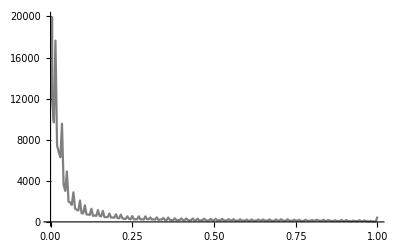

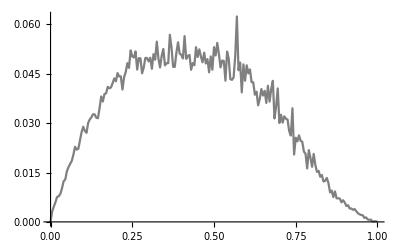

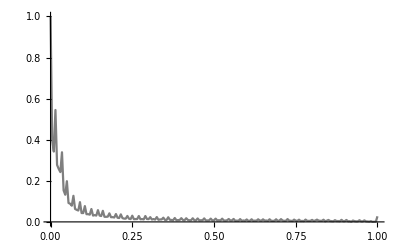

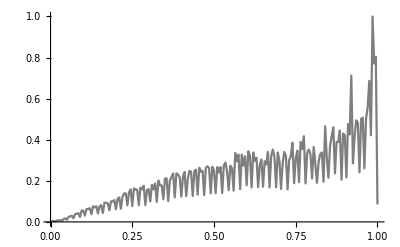

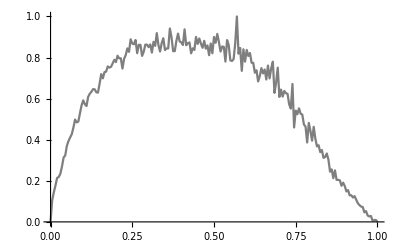

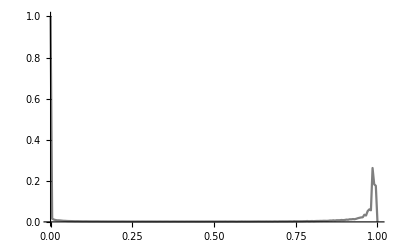

```mathematica
x=Take[h[[1]],Length[h[[1]]]-1];
y=h[[2]];
ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"]
ListLinePlot[Transpose[{x,stds}],ColorFunction->(GrayLevel[#]&),PlotLegends->"volatility histogram"]
ListLinePlot[Transpose[{intensityfunction,op2}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"intensity transfer function"]
ListLinePlot[Transpose[{intensityfunction,op}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"inverted intensity transfer function"]
ListLinePlot[Transpose[{intensityfunction,op4}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"volatility transfer function"]
ListLinePlot[Transpose[{intensityfunction,op3}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"inverted volatility transfer function"]
```

```mathematica
opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@rgbfunction[#],opacityfunction[#]]&/@intensityfunction;
colors=RGBColor/@rgba;
colorfunction=(Blend[Transpose[{intensityfunction,colors}], #1] & );
img=Image3D[d[[i]],ColorFunction->colorfunction];
```

```mathematica
tf=Import["E:\\_time_varying_data\\SmokeSim\\DSSmokeSideways100500\\dsSmoke.159.tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
colorfunction=(Blend[Transpose[{intensity,colors}], #1] & );
img=Image3D[d[[i]],ColorFunction->colorfunction];
```

```mathematica
opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@rgbfunction[#],opacityfunction[#]]&/@intensityfunction;
denormalized=(IntegerPart[255#]&)/@rgba;
r=Transpose[{intensityfunction,denormalized}]//Flatten[#]&/@#&;
strlist={ToString[#[[1]]],ToString[#[[2]]],ToString[#[[3]]],ToString[#[[4]]],ToString[#[[5]]]}&/@r;

alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({intensity=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[NotebookDirectory[]<>"smoke"<>IntegerString[160-1,10,3]<>"_201bins.tfi",xml, "XML"];
```

```mathematica
(* unwanted opacity 0.0409807, 0.0400936, 0.0326559 in 15.png, 16.png, 22.png *)
```

```mathematica
i=160;
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//RGBColor/@#&;
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );

start=1+offset;end=500;step=32;
start=1;
Do[
end2=Min[j+step-1,end];
Module[{result,a,h,intensityfunction,sum,hist,probability,entropy,op,opacityfunction,rgba,denormalized,r,strlist,alphaMode,gammaValue,domain,threshold,k,intensity,split,colorL,keylist,keys,TransFuncIntensity,VoreenData},
result=ParallelTable[
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[h[[2]]]-1)];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;

sum:=Total[h[[2]]];
probability[i_]:=N[h[[2]][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];If[p≠0,-p*Log[p],0]];
op=Module[{t},t=entropy[#];If[t!=0,1./t,0]]&/@intensityfunction//Rescale;

opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@rgbfunction[#],opacityfunction[#]]&/@intensityfunction;
denormalized=(IntegerPart[255#]&)/@rgba;
r=Transpose[{intensityfunction,denormalized}]//Flatten[#]&/@#&;
strlist=({ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&)@@@r;

alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({intensity=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}]
,{i,j,end2}];
num=Range[j,end2];
MapIndexed[
Export[NotebookDirectory[]<>"tf\\"<>IntegerString[num[[First[#2]]]-1,10,3]<>".tfi",#, "XML"]&,result]
]
,{j,start,end,step}]
```

```mathematica
i=160;
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[h[[2]]]-1)];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;

list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
b=Flatten[ImageData[std]];
numofbins=Length[h[[2]]]-1;
bins=ConstantArray[0,Length[h[[2]]]];
sumstd=ConstantArray[0,Length[h[[2]]]];
Table[j=IntegerPart[a[[i]]*numofbins]+1;bins[[j]]++;sumstd[[j]]+=b[[i]],{i,1,Length[a]}];
stds=Table[If[bins[[i]]≠0,sumstd[[i]]/bins[[i]],0],{i,1,Length[bins]}];
volatility[i_]:=N[stds[[hist[i]]]];
temporalentropy[i_]:=Module[{p},p=volatility[i];If[p≠0,-p*Log[p],0]];
op=temporalentropy[#]&/@intensityfunction//Rescale;

opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@rgbfunction[#],opacityfunction[#]]&/@intensityfunction;
denormalized=(IntegerPart[255#]&)/@rgba;
r=Transpose[{intensityfunction,denormalized}]//Flatten[#]&/@#&;
(*strlist={ToString[#[[1]]],ToString[#[[2]]],ToString[#[[3]]],ToString[#[[4]]],ToString[#[[5]]]}&/@r;*)
strlist=({ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&)@@@r;

alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({intensity=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[NotebookDirectory[]<>"std_tf\\"<>IntegerString[i-1,10,3]<>".tfi",xml, "XML"];
```

```mathematica
i=160;
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//RGBColor/@#&;
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );

start=1+offset;end=500;step=32;
Do[
end2=Min[j+step-1,end];
Module[{result,a,h,intensityfunction,hist,op,list,std,b,numofbins,bins,sumstd,stds,volatility,temporalentropy,opacityfunction,rgba,denormalized,r,strlist,alphaMode,gammaValue,domain,threshold,k,intensity,split,colorL,keylist,keys,TransFuncIntensity,VoreenData},
result=ParallelTable[
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[h[[2]]]-1)];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;

list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
b=Flatten[ImageData[std]];
numofbins=Length[h[[2]]]-1;
bins=ConstantArray[0,Length[h[[2]]]];
sumstd=ConstantArray[0,Length[h[[2]]]];
Table[j=IntegerPart[a[[i]]*numofbins]+1;bins[[j]]++;sumstd[[j]]+=b[[i]],{i,1,Length[a]}];
stds=Table[If[bins[[i]]≠0,sumstd[[i]]/bins[[i]],0],{i,1,Length[bins]}];
volatility[i_]:=N[stds[[hist[i]]]];
temporalentropy[i_]:=Module[{p},p=volatility[i];If[p≠0,-p*Log[p],0]];
op=temporalentropy[#]&/@intensityfunction//Rescale;

opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@rgbfunction[#],opacityfunction[#]]&/@intensityfunction;
denormalized=(IntegerPart[255#]&)/@rgba;
r=Transpose[{intensityfunction,denormalized}]//Flatten[#]&/@#&;
strlist=({ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&)@@@r;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({intensity=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}]
,{i,j,end2}];
num=Range[j,end2];
MapIndexed[
Export[NotebookDirectory[]<>"std_tf\\"<>IntegerString[num[[First[#2]]]-1,10,3]<>".tfi",#, "XML"]&,result]
]
,{j,start,end,step}]
```

```mathematica
Do[Module[{tf,intensity,r,g,b,a,rgba,colors,colorfunction,img},
tf=Import[NotebookDirectory[]<>"std_tf\\"<>IntegerString[i-1,10,3]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
colorfunction=(Blend[Transpose[{intensity,colors}], #1] & );
img=Image3D[d[[i]],ColorFunction->colorfunction];
Export[NotebookDirectory[]<>"smoke_std_tf\\"<>IntegerString[i-1,10,3]<>".png",img,ImageSize->640]
]
,{i,1+offset,500}]
```

```mathematica
Do[Module[{tf,intensity,r,g,b,a,rgba,colors,colorfunction,img},
tf=Import[NotebookDirectory[]<>"tf\\"<>IntegerString[i-1,10,3]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
colorfunction=(Blend[Transpose[{intensity,colors}], #1] & );
img=Image3D[d[[i]],ColorFunction->colorfunction];
Export[NotebookDirectory[]<>"smoke_entropy_tf\\"<>IntegerString[i-1,10,3]<>".png",img,ImageSize->640]
]
,{i,1,500}]
```

```mathematica
Do[Module[{tf,intensity,r,g,b,a,rgba,colors,colorfunction,img},
tf=Import["E:\\_time_varying_data\\SmokeSim\\DSSmokeSideways100500\\dsSmoke."<>IntegerString[i-1,10,3]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
colorfunction=(Blend[Transpose[{intensity,colors}], #1] & );
img=Image3D[d[[i]],ColorFunction->colorfunction];
Export[NotebookDirectory[]<>"smoke_intensity_tf\\"<>IntegerString[i-1,10,3]<>".png",img,ImageSize->640]
]
,{i,1,500}]
```